Тема 10. Використання диференціального числення.

Завдання 1. Графік дотичної.

Використовуючи систему «Mathematica», скласти рівняння дотичної до кривої в точці з абсцисою х0. Побудувати графіки функції і її дотичної в цій точці. Діапазони зміни x на графіках кривої та дотичної підбирати самостійно.

```mathematica
y[x_]=x^2+8*√x-32;
```

```mathematica
y1[x_]=Simplify[D[y[x],x]];
x0=4;
Y[x_]=y[x0]+y1[x0]*(x-x0)
```

10 (-4+x)

```mathematica
p1=Plot[y[x],{x,6,2},PlotStyle->{Black,Thickness[0.01]}];
```

```mathematica
p2=Plot[Y[x],{x,x0-1,x0+1},PlotStyle->{Red,Thickness[0.01]}];
```

```mathematica
p3=ListPlot[{{x0,y[x0]}},PlotStyle->{Blue,PointSize[0.05]}];
```

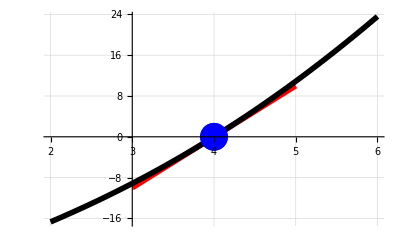

```mathematica
Show[p2,p1,p3,PlotRange->All,GridLines->Automatic]
```

Завдання 2. Дотична та нормаль до параметричної кривої.

Використовуючи систему «Mathematica», в зазначеній точці скласти рівняння дотичної та нормалі до параметрично заданої кривої. Побудувати графіки кривої, зображення точки дотику, а також графіки дотичної і нормалі в цій точці. В кожному варіанті при побудові кривої (графічний об’єкт p1) діапазони зміни параметра t підбирати так, щоб крива в околі точки дотику відображала свої характерні ділянки.

```mathematica
Remove[t]
```

```mathematica
x[t_]=3*t-t^2;
y[t_]=2*t-t^3;
t0=-0.25;
xt=x[t0]+t*x'[t0]
yt=y[t0]+t*y'[t0]
```

-0.8125+3.5 t

-0.484375+1.8125 t

```mathematica
xn[t_]=x[t0]+t*y'[t0]
```

-0.8125+1.8125 t

```mathematica
yn[t_]=y[t0]-t*x'[t0]
```

-0.484375-3.5 t

```mathematica
p1 = ParametricPlot[{x[t],y[t]},{t,-3,3},AspectRatio->Automatic, PlotStyle->Thickness[0.02]];
```

```mathematica
p2=Graphics[{Green,Disk[{x[t0],y[t0]},0.15]}];
```

```mathematica
p3= ParametricPlot[{xt[t],yt[t]},{t,-3,3},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
p4= ParametricPlot[{xn[t],yn[t]},{t,-3,3},PlotStyle->{Blue,Thickness[0.01]}];
```

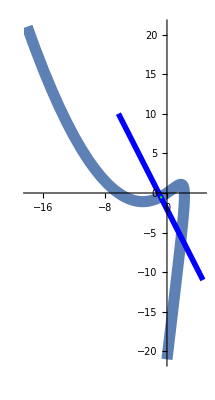

```mathematica
Show[p1,p3,p4,p2,PlotRange->All]
```

Завдання 3. Асимптоти.

Використовуючи систему «Mathematica», знайти асимптоти функції . Побудувати графік функції та всі її похилі і горизонтальні асимптоти. Якщо у функції є вертикальні асимптоти в точках , то ці точки виключити з графіка.

```mathematica
f[x_]=(4*x^2+9)/(4*x+8);
a=Limit[f[x]/x,x->∞]
b=Limit[f[x]-a*x,x->∞]
```

1

-2

```mathematica
Solve[4*x+8==0,x,Reals]
```

{{x→-2}}

```mathematica
Limit[f[x],x->-2]
```

Indeterminate

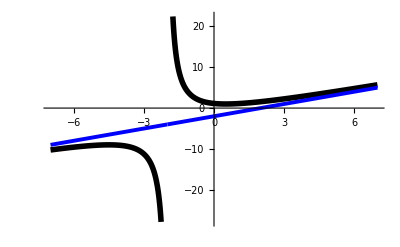

```mathematica
Plot[{f[x],a*x+b},{x,-7,7}, PlotStyle->{{Black,Thickness[0.01]},{Blue,Thickness[0.007]}},Exclusions->{-2}]
```

Завдання 4. Дотична і нормаль до кривої, яка задана неявно.

Використовуючи систему «Mathematica», скласти рівняння дотичної та нормалі до кривої, яка задана неявно. Побудувати графіки кривої, її дотичної та нормалі в точці, яку вибрати самостійно. Інтервали по x і y для зображення кривих в кожному варіанті підбирати окремо.

```mathematica
Remove[x,y,F,x0,y0]
```

```mathematica
F[x_,y_]=14*x^2+24*x*y+21*y^2-4*x+18*y-139;
pc1=ContourPlot[F[x,y]==0,{x,-6,6},{y,-6,6},ContourStyle->{Black,Thickness[0.01]}];
x0=1;
```

```mathematica
rez=N[Solve[F[x0,y]==0,y]]
```

{{y→-3.67261},{y→1.67261}}

```mathematica
y0=rez[[2]][[1,2]]
```

1.67261

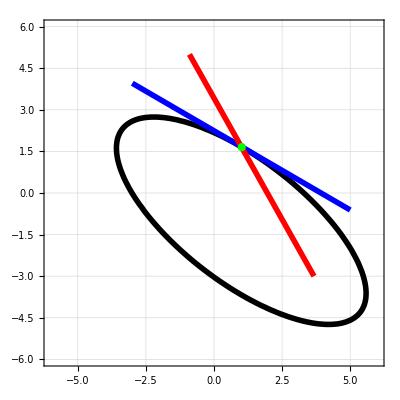

```mathematica
eqT=Derivative[1,0][F][x0,y0](x-x0)+Derivative[0,1][F][x0,y0](y-y0);
eqN=Derivative[1,0][F][x0,y0](y-y0)+Derivative[0,1][F][x0,y0](x-x0);
pc2=ContourPlot[{eqT==0,eqN==0},{x,x0-4,x0+4},{y,x0-4,x0+4},ContourStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}}];
pt=Graphics[{Green,Disk[{x0,y0},0.15]}];
Show[pc1,pc2,pt,AspectRatio->Automatic,GridLines->Automatic]
```

Завдання 5. Найбільше та найменше значення функції на відрізку.

Використовуючи систему «Mathematica», знайти найбільше та найменше значення функції на заданому відрізку. Побудувати графік функції і знайти точки максимуму і мінімуму першим способом. Перевірити отриманий розв’язок, знайшовши і побудувавши точки максимуму і мінімуму другим способом

```mathematica
Remove[x,y];
y[x_]=(2*(x^2+3))/(x^2-2x+5);
a=-3;
b=5;
s=NSolve[y'[x]==0,x,Reals];
{x1,x2}=x/.s
```

{-1.,3.}

```mathematica
{y''[x1],y''[x2]}
```

{0.25,-0.25}

```mathematica
{y[x1],y[x2]}
```

{1.,3.}

```mathematica
{y[a],y[b]}
```

{6/5,14/5}

```mathematica
Xmin=x1;
Ymin=y[x1];
Xmax=x2;
Ymax=y[x2];
```

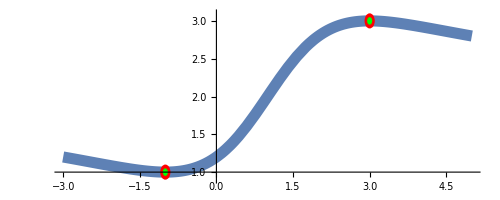

```mathematica
p1 = Plot[y[x],{x,a,b},PlotStyle->Thickness[0.02],AspectRatio->Automatic];
pt=Graphics[{Red,Disk[{Xmin,Ymin},0.1],Disk[{Xmax,Ymax},0.1]}];
mn=Minimize[{y[x],a≤x≤b},x];
{ymin,xmin}={mn[[1]],mn[[2,1,2]]};
mx=Maximize[{y[x],a≤x≤b},x];
{ymax,xmax}={mx[[1]],mx[[2,1,2]]};
pm=Graphics[{Green,Disk[{xmin,ymin},0.05],Disk[{xmax,ymax},0.05]}];
Show[p1,pt,pm,PlotRange->All]
```

Завдання 6. Частинні похідні. Нормаль до поверхні.

Використовуючи систему «Mathematica», обчислити частинні похідні першого і другого порядків функції z(x, y) . Побудувати графік функції і вектор нормалі до її поверхні в заданій точці (x0,y0) . Щоб нормаль до поверхні виглядала як нормаль, підібрати пропорції довжин осей графіка, використовуючи опцію BoxRatios.

```mathematica
Remove[x,y,z]
```

```mathematica
z[x_,y_]=(2*x+3*y)/(10+(x-y)^2);
zx[x_,y_]=Simplify[D[z[x,y],x]]
zy[x_,y_]=Simplify[D[z[x,y],y]]
```

-(2 (-10+x^2+3 x y-4 y^2))/((10+x^2-2 x y+y^2)^2)

(30+7 x^2-4 x y-3 y^2)/((10+x^2-2 x y+y^2)^2)

```mathematica
Simplify[D[z[x,y],{x,2}]]
```

(2 (2 x^3+9 x^2 y-12 x (5+2 y^2)+y (10+13 y^2)))/((10+x^2-2 x y+y^2)^3)

```mathematica
Simplify[D[z[x,y],x,y]]
```

(2 (-7 x^3+6 x^2 y-8 y (-5+y^2)+x (10+9 y^2)))/((10+x^2-2 x y+y^2)^3)

```mathematica
Simplify[D[z[x,y],{y,2}]]
```

(2 (12 x^3-21 x^2 y+3 y (-30+y^2)+x (40+6 y^2)))/((10+x^2-2 x y+y^2)^3)

```mathematica
x0=0.5;
y0=0.5;
P={x0,y0,z[x0,y0]}
```

{0.5,0.5,0.25}

```mathematica
n={zx[x0,y0],zy[x0,y0],-1}
```

{0.2,0.3,-1}

```mathematica
p1=Plot3D[z[x,y],{x,-1,1},{y,-1,1},PlotRange->All,Mesh->None];
p2=Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{P,P+n}]}];
Show[p1,p2,BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-